```mathematica
R = √2 ;(* NB: line drawing algorithm only considers neighbor pixels, but distances are in (-√2, √2) *)
Ω = π ;(* = (2π/T)/2; spatial extent T = 1 pixel *)
M = 3; (* cubic polynomials *)
ψ[m_, x_, y_] :=2 π Integrate[r^(m+1)BesselJ[0, r  Norm[{x,y}]],{r, 0, R}]
Φ = Table[(2π)^2 (2 π R^(k+l+2))/(k+l+2), {k,0, M}, {l, 0, M}]
Ψ = Table[ NIntegrate[ψ[k,x,y] ψ[l,x,y], {x, -Ω, Ω}, {y, -Ω, Ω}], {k, 0, M}, {l, 0, M}]
```

{{8 π^3,(16 √2 π^3)/3,8 π^3,(32 √2 π^3)/5},{(16 √2 π^3)/3,8 π^3,(32 √2 π^3)/5,(32 π^3)/3},{8 π^3,(32 √2 π^3)/5,(32 π^3)/3,(64 √2 π^3)/7},{(32 √2 π^3)/5,(32 π^3)/3,(64 √2 π^3)/7,16 π^3}}

{{213.786,184.293,182.737,196.198},{184.293,175.482,184.642,206.148},{182.737,184.642,200.547,228.356},{196.198,206.148,228.356,263.123}}

```mathematica
e = Eigensystem[Inverse[Φ].Ψ];
largestEigenval = e[[1]][[1]] (* = energy concentration (this assumes EVs are sorted) *)
h = e[[2]][[1]] (* eigenvector for largestEigenval *)
```

0.992473

{0.6307,0.012625,-0.716862,0.29693}

{0.59994,0.0120092,-0.6819,0.282449}

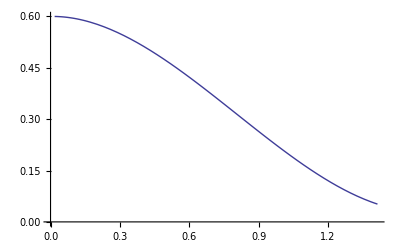

```mathematica
filt[h_,x_] :=  h[[1]] + h[[2]] x + h[[3]] x^2 + h[[4]] x^3
hn =  h/(2 Integrate[filt[h, x], {x, 0,R}]) (* unit integral over -R..R *)
Plot[filt[hn,x], {x, 0,R},PlotRange-> {0,filt[hn,0]}]
```

```mathematica
(****************************************************
now convolve the h kernel with a line to obtain RLT *)
cfilt[x_] := If[Abs[x] ≤ R, filt[hn,x], 0] (* clamped *)
trans[r_] := 2 Integrate[cfilt[Norm[{r,x}]], {x, 0, R}]
```

{{0,1.},{0.00141421,0.999998},{0.00282843,0.999992},{0.00424264,0.999981},{0.00565685,0.999967},{0.00707107,0.999948},{0.00848528,0.999925},{0.00989949,0.999898},{0.0113137,0.999866},{0.0127279,0.99983},{0.0141421,0.99979},{0.0155563,0.999746},{0.0169706,0.999698},{0.0183848,0.999645},{0.019799,0.999588},{0.0212132,0.999526},{0.0226274,0.999461},{0.0240416,0.999391},{0.0254558,0.999316},{0.0268701,0.999238},{0.0282843,0.999155},{0.0296985,0.999068},{0.0311127,0.998977},{0.0325269,0.998881},{0.0339411,0.998782},{0.0353553,0.998677},{0.0367696,0.998569},{0.0381838,0.998456},{0.039598,0.998339},{0.0410122,0.998218},{0.0424264,0.998092},{0.0438406,0.997963},{0.0452548,0.997829},{0.046669,0.99769},{0.0480833,0.997547},{0.0494975,0.997401},{0.0509117,0.997249},{0.0523259,0.997094},{0.0537401,0.996934},{0.0551543,0.99677},{0.0565685,0.996602},{0.0579828,0.996429},{0.059397,0.996253},{0.0608112,0.996071},{0.0622254,0.995886},{0.0636396,0.995697},{0.0650538,0.995503},{0.066468,0.995305},{0.0678823,0.995102},{0.0692965,0.994896},{0.0707107,0.994685},{0.0721249,0.99447},{0.0735391,0.994251},{0.0749533,0.994027},{0.0763675,0.993799},{0.0777817,0.993567},{0.079196,0.993331},{0.0806102,0.993091},{0.0820244,0.992846},{0.0834386,0.992597},{0.0848528,0.992344},{0.086267,0.992087},{0.0876812,0.991825},{0.0890955,0.991559},{0.0905097,0.991289},{0.0919239,0.991015},{0.0933381,0.990737},{0.0947523,0.990454},{0.0961665,0.990167},{0.0975807,0.989877},{0.0989949,0.989581},{0.100409,0.989282},{0.101823,0.988979},{0.103238,0.988671},{0.104652,0.988359},{0.106066,0.988043},{0.10748,0.987723},{0.108894,0.987399},{0.110309,0.98707},{0.111723,0.986738},{0.113137,0.986401},{0.114551,0.98606},{0.115966,0.985715},{0.11738,0.985366},{0.118794,0.985013},{0.120208,0.984656},{0.121622,0.984294},{0.123037,0.983929},{0.124451,0.983559},{0.125865,0.983185},{0.127279,0.982807},{0.128693,0.982425},{0.130108,0.982039},{0.131522,0.981649},{0.132936,0.981255},{0.13435,0.980856},{0.135765,0.980454},{0.137179,0.980048},{0.138593,0.979637},{0.140007,0.979222},{0.141421,0.978804},{0.142836,0.978381},{0.14425,0.977954},{0.145664,0.977524},{0.147078,0.977089},{0.148492,0.97665},{0.149907,0.976207},{0.151321,0.975761},{0.152735,0.97531},{0.154149,0.974855},{0.155563,0.974396},{0.156978,0.973933},{0.158392,0.973467},{0.159806,0.972996},{0.16122,0.972521},{0.162635,0.972042},{0.164049,0.97156},{0.165463,0.971073},{0.166877,0.970582},{0.168291,0.970088},{0.169706,0.969589},{0.17112,0.969087},{0.172534,0.968581},{0.173948,0.968071},{0.175362,0.967556},{0.176777,0.967038},{0.178191,0.966516},{0.179605,0.96599},{0.181019,0.965461},{0.182434,0.964927},{0.183848,0.96439},{0.185262,0.963848},{0.186676,0.963303},{0.18809,0.962754},{0.189505,0.962201},{0.190919,0.961644},{0.192333,0.961083},{0.193747,0.960519},{0.195161,0.959951},{0.196576,0.959378},{0.19799,0.958802},{0.199404,0.958223},{0.200818,0.957639},{0.202233,0.957052},{0.203647,0.956461},{0.205061,0.955866},{0.206475,0.955267},{0.207889,0.954664},{0.209304,0.954058},{0.210718,0.953448},{0.212132,0.952835},{0.213546,0.952217},{0.21496,0.951596},{0.216375,0.950971},{0.217789,0.950342},{0.219203,0.94971},{0.220617,0.949074},{0.222032,0.948434},{0.223446,0.947791},{0.22486,0.947143},{0.226274,0.946493},{0.227688,0.945838},{0.229103,0.94518},{0.230517,0.944518},{0.231931,0.943853},{0.233345,0.943184},{0.234759,0.942511},{0.236174,0.941835},{0.237588,0.941155},{0.239002,0.940471},{0.240416,0.939784},{0.241831,0.939093},{0.243245,0.938399},{0.244659,0.937701},{0.246073,0.936999},{0.247487,0.936294},{0.248902,0.935585},{0.250316,0.934873},{0.25173,0.934157},{0.253144,0.933438},{0.254558,0.932715},{0.255973,0.931989},{0.257387,0.931259},{0.258801,0.930526},{0.260215,0.929789},{0.26163,0.929048},{0.263044,0.928304},{0.264458,0.927557},{0.265872,0.926806},{0.267286,0.926052},{0.268701,0.925294},{0.270115,0.924533},{0.271529,0.923769},{0.272943,0.923001},{0.274357,0.922229},{0.275772,0.921454},{0.277186,0.920676},{0.2786,0.919895},{0.280014,0.91911},{0.281428,0.918321},{0.282843,0.917529},{0.284257,0.916734},{0.285671,0.915936},{0.287085,0.915134},{0.2885,0.914329},{0.289914,0.91352},{0.291328,0.912708},{0.292742,0.911893},{0.294156,0.911075},{0.295571,0.910253},{0.296985,0.909428},{0.298399,0.9086},{0.299813,0.907768},{0.301227,0.906933},{0.302642,0.906095},{0.304056,0.905254},{0.30547,0.904409},{0.306884,0.903562},{0.308299,0.902711},{0.309713,0.901856},{0.311127,0.900999},{0.312541,0.900138},{0.313955,0.899274},{0.31537,0.898407},{0.316784,0.897537},{0.318198,0.896664},{0.319612,0.895787},{0.321026,0.894908},{0.322441,0.894025},{0.323855,0.893139},{0.325269,0.89225},{0.326683,0.891358},{0.328098,0.890463},{0.329512,0.889564},{0.330926,0.888663},{0.33234,0.887759},{0.333754,0.886851},{0.335169,0.88594},{0.336583,0.885027},{0.337997,0.88411},{0.339411,0.883191},{0.340825,0.882268},{0.34224,0.881342},{0.343654,0.880413},{0.345068,0.879482},{0.346482,0.878547},{0.347897,0.877609},{0.349311,0.876669},{0.350725,0.875725},{0.352139,0.874778},{0.353553,0.873829},{0.354968,0.872877},{0.356382,0.871921},{0.357796,0.870963},{0.35921,0.870002},{0.360624,0.869038},{0.362039,0.868071},{0.363453,0.867101},{0.364867,0.866129},{0.366281,0.865153},{0.367696,0.864175},{0.36911,0.863193},{0.370524,0.862209},{0.371938,0.861223},{0.373352,0.860233},{0.374767,0.859241},{0.376181,0.858245},{0.377595,0.857247},{0.379009,0.856246},{0.380423,0.855243},{0.381838,0.854237},{0.383252,0.853228},{0.384666,0.852216},{0.38608,0.851201},{0.387495,0.850184},{0.388909,0.849164},{0.390323,0.848142},{0.391737,0.847116},{0.393151,0.846088},{0.394566,0.845058},{0.39598,0.844024},{0.397394,0.842988},{0.398808,0.84195},{0.400222,0.840909},{0.401637,0.839865},{0.403051,0.838818},{0.404465,0.837769},{0.405879,0.836718},{0.407294,0.835663},{0.408708,0.834607},{0.410122,0.833547},{0.411536,0.832485},{0.41295,0.831421},{0.414365,0.830354},{0.415779,0.829285},{0.417193,0.828213},{0.418607,0.827138},{0.420021,0.826061},{0.421436,0.824982},{0.42285,0.8239},{0.424264,0.822815},{0.425678,0.821728},{0.427092,0.820639},{0.428507,0.819547},{0.429921,0.818453},{0.431335,0.817357},{0.432749,0.816258},{0.434164,0.815156},{0.435578,0.814052},{0.436992,0.812946},{0.438406,0.811838},{0.43982,0.810727},{0.441235,0.809614},{0.442649,0.808498},{0.444063,0.80738},{0.445477,0.80626},{0.446891,0.805138},{0.448306,0.804013},{0.44972,0.802886},{0.451134,0.801757},{0.452548,0.800625},{0.453963,0.799491},{0.455377,0.798355},{0.456791,0.797217},{0.458205,0.796076},{0.459619,0.794934},{0.461034,0.793789},{0.462448,0.792641},{0.463862,0.791492},{0.465276,0.790341},{0.46669,0.789187},{0.468105,0.788031},{0.469519,0.786873},{0.470933,0.785713},{0.472347,0.784551},{0.473762,0.783387},{0.475176,0.78222},{0.47659,0.781052},{0.478004,0.779881},{0.479418,0.778708},{0.480833,0.777534},{0.482247,0.776357},{0.483661,0.775178},{0.485075,0.773997},{0.486489,0.772814},{0.487904,0.77163},{0.489318,0.770443},{0.490732,0.769254},{0.492146,0.768063},{0.493561,0.76687},{0.494975,0.765675},{0.496389,0.764479},{0.497803,0.76328},{0.499217,0.76208},{0.500632,0.760877},{0.502046,0.759673},{0.50346,0.758466},{0.504874,0.757258},{0.506288,0.756048},{0.507703,0.754836},{0.509117,0.753623},{0.510531,0.752407},{0.511945,0.75119},{0.51336,0.74997},{0.514774,0.748749},{0.516188,0.747526},{0.517602,0.746302},{0.519016,0.745075},{0.520431,0.743847},{0.521845,0.742617},{0.523259,0.741386},{0.524673,0.740152},{0.526087,0.738917},{0.527502,0.73768},{0.528916,0.736441},{0.53033,0.735201},{0.531744,0.733959},{0.533159,0.732715},{0.534573,0.73147},{0.535987,0.730223},{0.537401,0.728975},{0.538815,0.727724},{0.54023,0.726473},{0.541644,0.725219},{0.543058,0.723964},{0.544472,0.722707},{0.545886,0.721449},{0.547301,0.720189},{0.548715,0.718928},{0.550129,0.717665},{0.551543,0.7164},{0.552958,0.715135},{0.554372,0.713867},{0.555786,0.712598},{0.5572,0.711327},{0.558614,0.710056},{0.560029,0.708782},{0.561443,0.707507},{0.562857,0.706231},{0.564271,0.704953},{0.565685,0.703674},{0.5671,0.702393},{0.568514,0.701111},{0.569928,0.699828},{0.571342,0.698543},{0.572756,0.697256},{0.574171,0.695969},{0.575585,0.69468},{0.576999,0.69339},{0.578413,0.692098},{0.579828,0.690805},{0.581242,0.689511},{0.582656,0.688215},{0.58407,0.686918},{0.585484,0.68562},{0.586899,0.684321},{0.588313,0.68302},{0.589727,0.681718},{0.591141,0.680415},{0.592555,0.67911},{0.59397,0.677805},{0.595384,0.676498},{0.596798,0.67519},{0.598212,0.673881},{0.599627,0.67257},{0.601041,0.671259},{0.602455,0.669946},{0.603869,0.668632},{0.605283,0.667317},{0.606698,0.666001},{0.608112,0.664684},{0.609526,0.663366},{0.61094,0.662046},{0.612354,0.660726},{0.613769,0.659404},{0.615183,0.658082},{0.616597,0.656758},{0.618011,0.655434},{0.619426,0.654108},{0.62084,0.652781},{0.622254,0.651454},{0.623668,0.650125},{0.625082,0.648795},{0.626497,0.647465},{0.627911,0.646133},{0.629325,0.6448},{0.630739,0.643467},{0.632153,0.642132},{0.633568,0.640797},{0.634982,0.639461},{0.636396,0.638124},{0.63781,0.636786},{0.639225,0.635447},{0.640639,0.634107},{0.642053,0.632767},{0.643467,0.631425},{0.644881,0.630083},{0.646296,0.62874},{0.64771,0.627396},{0.649124,0.626051},{0.650538,0.624706},{0.651952,0.623359},{0.653367,0.622012},{0.654781,0.620665},{0.656195,0.619316},{0.657609,0.617967},{0.659024,0.616617},{0.660438,0.615266},{0.661852,0.613915},{0.663266,0.612563},{0.66468,0.61121},{0.666095,0.609857},{0.667509,0.608503},{0.668923,0.607148},{0.670337,0.605792},{0.671751,0.604436},{0.673166,0.60308},{0.67458,0.601723},{0.675994,0.600365},{0.677408,0.599006},{0.678823,0.597647},{0.680237,0.596288},{0.681651,0.594928},{0.683065,0.593567},{0.684479,0.592206},{0.685894,0.590845},{0.687308,0.589482},{0.688722,0.58812},{0.690136,0.586757},{0.69155,0.585393},{0.692965,0.584029},{0.694379,0.582664},{0.695793,0.581299},{0.697207,0.579934},{0.698621,0.578568},{0.700036,0.577202},{0.70145,0.575835},{0.702864,0.574468},{0.704278,0.573101},{0.705693,0.571733},{0.707107,0.570365},{0.708521,0.568996},{0.709935,0.567628},{0.711349,0.566258},{0.712764,0.564889},{0.714178,0.563519},{0.715592,0.562149},{0.717006,0.560779},{0.71842,0.559408},{0.719835,0.558037},{0.721249,0.556666},{0.722663,0.555295},{0.724077,0.553923},{0.725492,0.552552},{0.726906,0.55118},{0.72832,0.549807},{0.729734,0.548435},{0.731148,0.547062},{0.732563,0.54569},{0.733977,0.544317},{0.735391,0.542944},{0.736805,0.54157},{0.738219,0.540197},{0.739634,0.538824},{0.741048,0.53745},{0.742462,0.536077},{0.743876,0.534703},{0.745291,0.533329},{0.746705,0.531955},{0.748119,0.530582},{0.749533,0.529208},{0.750947,0.527834},{0.752362,0.52646},{0.753776,0.525086},{0.75519,0.523712},{0.756604,0.522338},{0.758018,0.520964},{0.759433,0.51959},{0.760847,0.518216},{0.762261,0.516842},{0.763675,0.515469},{0.76509,0.514095},{0.766504,0.512722},{0.767918,0.511348},{0.769332,0.509975},{0.770746,0.508601},{0.772161,0.507228},{0.773575,0.505855},{0.774989,0.504483},{0.776403,0.50311},{0.777817,0.501737},{0.779232,0.500365},{0.780646,0.498993},{0.78206,0.497621},{0.783474,0.496249},{0.784889,0.494878},{0.786303,0.493507},{0.787717,0.492136},{0.789131,0.490765},{0.790545,0.489395},{0.79196,0.488024},{0.793374,0.486654},{0.794788,0.485285},{0.796202,0.483915},{0.797616,0.482546},{0.799031,0.481178},{0.800445,0.479809},{0.801859,0.478441},{0.803273,0.477074},{0.804688,0.475706},{0.806102,0.47434},{0.807516,0.472973},{0.80893,0.471607},{0.810344,0.470241},{0.811759,0.468876},{0.813173,0.467511},{0.814587,0.466147},{0.816001,0.464783},{0.817415,0.463419},{0.81883,0.462056},{0.820244,0.460693},{0.821658,0.459331},{0.823072,0.45797},{0.824487,0.456609},{0.825901,0.455248},{0.827315,0.453888},{0.828729,0.452529},{0.830143,0.45117},{0.831558,0.449811},{0.832972,0.448453},{0.834386,0.447096},{0.8358,0.445739},{0.837214,0.444383},{0.838629,0.443028},{0.840043,0.441673},{0.841457,0.440319},{0.842871,0.438965},{0.844285,0.437612},{0.8457,0.43626},{0.847114,0.434909},{0.848528,0.433558},{0.849942,0.432207},{0.851357,0.430858},{0.852771,0.429509},{0.854185,0.428161},{0.855599,0.426814},{0.857013,0.425467},{0.858428,0.424121},{0.859842,0.422776},{0.861256,0.421432},{0.86267,0.420088},{0.864084,0.418745},{0.865499,0.417403},{0.866913,0.416062},{0.868327,0.414722},{0.869741,0.413382},{0.871156,0.412043},{0.87257,0.410705},{0.873984,0.409368},{0.875398,0.408032},{0.876812,0.406697},{0.878227,0.405362},{0.879641,0.404029},{0.881055,0.402696},{0.882469,0.401365},{0.883883,0.400034},{0.885298,0.398704},{0.886712,0.397375},{0.888126,0.396047},{0.88954,0.39472},{0.890955,0.393394},{0.892369,0.392069},{0.893783,0.390745},{0.895197,0.389422},{0.896611,0.3881},{0.898026,0.386779},{0.89944,0.385459},{0.900854,0.38414},{0.902268,0.382822},{0.903682,0.381505},{0.905097,0.380189},{0.906511,0.378874},{0.907925,0.37756},{0.909339,0.376248},{0.910754,0.374936},{0.912168,0.373626},{0.913582,0.372316},{0.914996,0.371008},{0.91641,0.369701},{0.917825,0.368395},{0.919239,0.367091},{0.920653,0.365787},{0.922067,0.364485},{0.923481,0.363183},{0.924896,0.361883},{0.92631,0.360584},{0.927724,0.359287},{0.929138,0.35799},{0.930553,0.356695},{0.931967,0.355401},{0.933381,0.354109},{0.934795,0.352817},{0.936209,0.351527},{0.937624,0.350238},{0.939038,0.34895},{0.940452,0.347664},{0.941866,0.346379},{0.94328,0.345095},{0.944695,0.343813},{0.946109,0.342531},{0.947523,0.341252},{0.948937,0.339973},{0.950352,0.338696},{0.951766,0.33742},{0.95318,0.336146},{0.954594,0.334873},{0.956008,0.333601},{0.957423,0.332331},{0.958837,0.331062},{0.960251,0.329795},{0.961665,0.328529},{0.963079,0.327264},{0.964494,0.326001},{0.965908,0.324739},{0.967322,0.323479},{0.968736,0.32222},{0.970151,0.320963},{0.971565,0.319707},{0.972979,0.318452},{0.974393,0.317199},{0.975807,0.315948},{0.977222,0.314698},{0.978636,0.31345},{0.98005,0.312203},{0.981464,0.310958},{0.982878,0.309714},{0.984293,0.308472},{0.985707,0.307231},{0.987121,0.305992},{0.988535,0.304754},{0.989949,0.303518},{0.991364,0.302284},{0.992778,0.301051},{0.994192,0.29982},{0.995606,0.29859},{0.997021,0.297362},{0.998435,0.296136},{0.999849,0.294911},{1.00126,0.293688},{1.00268,0.292467},{1.00409,0.291247},{1.00551,0.290029},{1.00692,0.288812},{1.00833,0.287598},{1.00975,0.286385},{1.01116,0.285173},{1.01258,0.283964},{1.01399,0.282756},{1.01541,0.281549},{1.01682,0.280345},{1.01823,0.279142},{1.01965,0.277941},{1.02106,0.276742},{1.02248,0.275544},{1.02389,0.274349},{1.0253,0.273155},{1.02672,0.271962},{1.02813,0.270772},{1.02955,0.269583},{1.03096,0.268396},{1.03238,0.267211},{1.03379,0.266028},{1.0352,0.264847},{1.03662,0.263667},{1.03803,0.262489},{1.03945,0.261313},{1.04086,0.260139},{1.04228,0.258967},{1.04369,0.257797},{1.0451,0.256628},{1.04652,0.255461},{1.04793,0.254297},{1.04935,0.253134},{1.05076,0.251973},{1.05217,0.250814},{1.05359,0.249657},{1.055,0.248501},{1.05642,0.247348},{1.05783,0.246196},{1.05925,0.245047},{1.06066,0.243899},{1.06207,0.242754},{1.06349,0.24161},{1.0649,0.240468},{1.06632,0.239329},{1.06773,0.238191},{1.06915,0.237055},{1.07056,0.235921},{1.07197,0.234789},{1.07339,0.233659},{1.0748,0.232531},{1.07622,0.231405},{1.07763,0.230282},{1.07904,0.22916},{1.08046,0.22804},{1.08187,0.226922},{1.08329,0.225806},{1.0847,0.224692},{1.08612,0.223581},{1.08753,0.222471},{1.08894,0.221363},{1.09036,0.220258},{1.09177,0.219154},{1.09319,0.218053},{1.0946,0.216953},{1.09602,0.215856},{1.09743,0.214761},{1.09884,0.213668},{1.10026,0.212577},{1.10167,0.211488},{1.10309,0.210401},{1.1045,0.209316},{1.10592,0.208234},{1.10733,0.207153},{1.10874,0.206075},{1.11016,0.204998},{1.11157,0.203924},{1.11299,0.202852},{1.1144,0.201782},{1.11581,0.200714},{1.11723,0.199649},{1.11864,0.198585},{1.12006,0.197524},{1.12147,0.196465},{1.12289,0.195408},{1.1243,0.194353},{1.12571,0.193301},{1.12713,0.19225},{1.12854,0.191202},{1.12996,0.190156},{1.13137,0.189112},{1.13279,0.18807},{1.1342,0.18703},{1.13561,0.185993},{1.13703,0.184958},{1.13844,0.183925},{1.13986,0.182894},{1.14127,0.181866},{1.14268,0.180839},{1.1441,0.179815},{1.14551,0.178793},{1.14693,0.177773},{1.14834,0.176756},{1.14976,0.175741},{1.15117,0.174728},{1.15258,0.173717},{1.154,0.172708},{1.15541,0.171702},{1.15683,0.170698},{1.15824,0.169696},{1.15966,0.168696},{1.16107,0.167699},{1.16248,0.166703},{1.1639,0.16571},{1.16531,0.16472},{1.16673,0.163731},{1.16814,0.162745},{1.16955,0.161761},{1.17097,0.160779},{1.17238,0.1598},{1.1738,0.158823},{1.17521,0.157848},{1.17663,0.156875},{1.17804,0.155904},{1.17945,0.154936},{1.18087,0.15397},{1.18228,0.153007},{1.1837,0.152045},{1.18511,0.151086},{1.18653,0.150129},{1.18794,0.149174},{1.18935,0.148222},{1.19077,0.147271},{1.19218,0.146323},{1.1936,0.145378},{1.19501,0.144434},{1.19642,0.143493},{1.19784,0.142554},{1.19925,0.141617},{1.20067,0.140683},{1.20208,0.139751},{1.2035,0.138821},{1.20491,0.137893},{1.20632,0.136967},{1.20774,0.136044},{1.20915,0.135123},{1.21057,0.134204},{1.21198,0.133287},{1.2134,0.132373},{1.21481,0.131461},{1.21622,0.130551},{1.21764,0.129643},{1.21905,0.128738},{1.22047,0.127834},{1.22188,0.126933},{1.22329,0.126034},{1.22471,0.125137},{1.22612,0.124243},{1.22754,0.12335},{1.22895,0.12246},{1.23037,0.121572},{1.23178,0.120686},{1.23319,0.119802},{1.23461,0.118921},{1.23602,0.118041},{1.23744,0.117164},{1.23885,0.116289},{1.24027,0.115416},{1.24168,0.114545},{1.24309,0.113676},{1.24451,0.112809},{1.24592,0.111944},{1.24734,0.111082},{1.24875,0.110221},{1.25016,0.109363},{1.25158,0.108506},{1.25299,0.107652},{1.25441,0.1068},{1.25582,0.105949},{1.25724,0.105101},{1.25865,0.104255},{1.26006,0.103411},{1.26148,0.102568},{1.26289,0.101728},{1.26431,0.100889},{1.26572,0.100053},{1.26714,0.0992183},{1.26855,0.0983856},{1.26996,0.0975548},{1.27138,0.0967259},{1.27279,0.0958988},{1.27421,0.0950735},{1.27562,0.0942501},{1.27703,0.0934285},{1.27845,0.0926087},{1.27986,0.0917906},{1.28128,0.0909743},{1.28269,0.0901597},{1.28411,0.0893468},{1.28552,0.0885355},{1.28693,0.087726},{1.28835,0.086918},{1.28976,0.0861117},{1.29118,0.0853069},{1.29259,0.0845037},{1.29401,0.0837021},{1.29542,0.0829019},{1.29683,0.0821032},{1.29825,0.081306},{1.29966,0.0805101},{1.30108,0.0797157},{1.30249,0.0789225},{1.3039,0.0781307},{1.30532,0.0773402},{1.30673,0.0765509},{1.30815,0.0757628},{1.30956,0.0749758},{1.31098,0.07419},{1.31239,0.0734052},{1.3138,0.0726215},{1.31522,0.0718387},{1.31663,0.0710568},{1.31805,0.0702759},{1.31946,0.0694958},{1.32088,0.0687164},{1.32229,0.0679377},{1.3237,0.0671597},{1.32512,0.0663823},{1.32653,0.0656055},{1.32795,0.064829},{1.32936,0.064053},{1.33077,0.0632773},{1.33219,0.0625018},{1.3336,0.0617265},{1.33502,0.0609512},{1.33643,0.0601759},{1.33785,0.0594005},{1.33926,0.0586249},{1.34067,0.057849},{1.34209,0.0570727},{1.3435,0.0562958},{1.34492,0.0555183},{1.34633,0.05474},{1.34775,0.0539608},{1.34916,0.0531806},{1.35057,0.0523992},{1.35199,0.0516164},{1.3534,0.050832},{1.35482,0.050046},{1.35623,0.0492581},{1.35765,0.0484681},{1.35906,0.0476759},{1.36047,0.0468811},{1.36189,0.0460835},{1.3633,0.0452829},{1.36472,0.044479},{1.36613,0.0436716},{1.36754,0.0428602},{1.36896,0.0420445},{1.37037,0.0412242},{1.37179,0.0403989},{1.3732,0.0395681},{1.37462,0.0387313},{1.37603,0.037888},{1.37744,0.0370377},{1.37886,0.0361797},{1.38027,0.0353133},{1.38169,0.0344377},{1.3831,0.0335521},{1.38452,0.0326555},{1.38593,0.0317468},{1.38734,0.0308249},{1.38876,0.0298883},{1.39017,0.0289354},{1.39159,0.0279644},{1.393,0.0269733},{1.39441,0.0259594},{1.39583,0.0249198},{1.39724,0.0238511},{1.39866,0.0227488},{1.40007,0.0216077},{1.40149,0.020421},{1.4029,0.01918},{1.40431,0.0178732},{1.40573,0.0164847},{1.40714,0.0149914},{1.40856,0.013358},{1.40997,0.0115246},{1.41139,0.00937427},{1.4128,0.0066036},{1.41421,0.}}

1.0014+0.00860678 x-1.24862 x^2+0.534384 x^3

0.781973

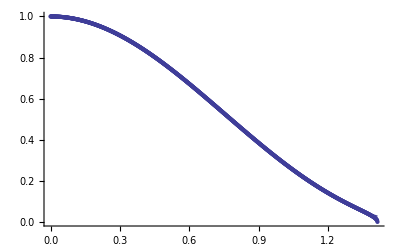

```mathematica
(* 100 would suffice; computing 1000 took about 2h *)
steps = 1000.0;
xAtStep[i_] := i R / steps
support = Table[0, {i,steps+1}, {j,2}];
For[i=0, i <= steps, i += 1, support[[i+1]] = {xAtStep[i], trans[xAtStep[i]]}]
support (* bulky, but useful for backup purposes *)
interp = Fit[support, {1,x,x^2,x^3}, x]
Integrate[interp, {x, 0, R}]
Show[ListPlot[support], Plot[interp, {x, 0, R}],PlotRange ->{0,1}]
```

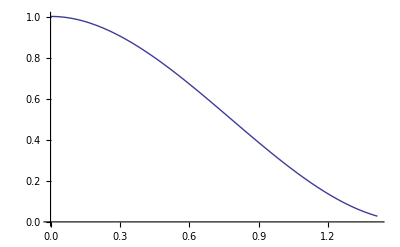

```mathematica
Plot[1.0014013169407334+0.00860678228060248 x-1.2486235927379503 x^2+0.5343841982754345 x^3, {x, 0, R}]
```